### Start choosing the example:

```mathematica
t=30;
beta = 0;
A = 0.2;
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.008364,Null}

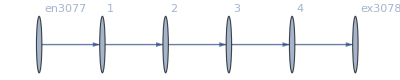

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j3079→80.,j3080→80.,j3081→80.,j3082→80.,j3083→80.,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80.,jt3091→80.,jt3092→0.,jt3093→80.,jt3094→0.,jt3095→80.,jt3096→0.,u3097→255.,u3098→175.,u3099→95.,u3100→15.,u3101→255.,u3102→175.,u3103→95.,u3104→15.,u3105→15.,u3106→255.|>

#### Non-linear case

I suppose we can drop the SameTest:

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.9871×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.9871×10^-17

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→22.7459,u3098→20.1639,u3099→17.582,u3100→15.,u3101→22.7459,u3102→20.1639,u3103→17.582,u3104→15.,u3105→15.,u3106→22.7459|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.00831×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.00831×10^-17

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→24.484,u3098→21.3227,u3099→18.1613,u3100→15.,u3101→24.484,u3102→21.3227,u3103→18.1613,u3104→15.,u3105→15.,u3106→24.484|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.23109×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.23109×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→30.0717,u3098→25.0478,u3099→20.0239,u3100→15.,u3101→30.0717,u3102→25.0478,u3103→20.0239,u3104→15.,u3105→15.,u3106→30.0717|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→149.898,u3098→104.932,u3099→59.966,u3100→15.,u3101→149.898,u3102→104.932,u3103→59.966,u3104→15.,u3105→15.,u3106→149.898|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.47684×10^-13

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→255.,u3098→175.,u3099→95.,u3100→15.,u3101→255.,u3102→175.,u3103→95.,u3104→15.,u3105→15.,u3106→255.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.4679×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.4679×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→1106.72,u3098→742.811,u3099→378.906,u3100→15.,u3101→1106.72,u3102→742.811,u3103→378.906,u3104→15.,u3105→15.,u3106→1106.72|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→68536.4,u3098→45695.9,u3099→22855.5,u3100→15.,u3101→68536.4,u3102→45695.9,u3103→22855.5,u3104→15.,u3105→15.,u3106→68536.4|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→870144.,u3098→580101.,u3099→290058.,u3100→15.,u3101→870144.,u3102→580101.,u3103→290058.,u3104→15.,u3105→15.,u3106→870144.|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→872843.,u3098→581900.,u3099→290958.,u3100→15.,u3101→872843.,u3102→581900.,u3103→290958.,u3104→15.,u3105→15.,u3106→872843.|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→1.01758×10^6,u3098→678389.,u3099→339202.,u3100→15.,u3101→1.01758×10^6,u3102→678389.,u3103→339202.,u3104→15.,u3105→15.,u3106→1.01758×10^6|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.92515×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.92515×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→1.1942×10^6,u3098→796137.,u3099→398076.,u3100→15.,u3101→1.1942×10^6,u3102→796137.,u3103→398076.,u3104→15.,u3105→15.,u3106→1.1942×10^6|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.63778×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.63778×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→1.66311×10^6,u3098→1.10875×10^6,u3099→554381.,u3100→15.,u3101→1.66311×10^6,u3102→1.10875×10^6,u3103→554381.,u3104→15.,u3105→15.,u3106→1.66311×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→4.96168×10^6,u3098→3.30779×10^6,u3099→1.6539×10^6,u3100→15.,u3101→4.96168×10^6,u3102→3.30779×10^6,u3103→1.6539×10^6,u3104→15.,u3105→15.,u3106→4.96168×10^6|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.38879×10^-16

«7 more identical outputs»

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→4.6785×10^7,u3098→3.119×10^7,u3099→1.5595×10^7,u3100→15.,u3101→4.6785×10^7,u3102→3.119×10^7,u3103→1.5595×10^7,u3104→15.,u3105→15.,u3106→4.6785×10^7|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.17196×10^-16

«7 more identical outputs»

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→7.21578×10^10,u3098→4.81052×10^10,u3099→2.40526×10^10,u3100→15.,u3101→7.21578×10^10,u3102→4.81052×10^10,u3103→2.40526×10^10,u3104→15.,u3105→15.,u3106→7.21578×10^10|>

```mathematica
alpha = 1.89;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.65439×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.65439×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.65439×10^-16

«7 more identical outputs»

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→6.26422×10^17,u3098→4.17614×10^17,u3099→2.08807×10^17,u3100→15.,u3101→6.26422×10^17,u3102→4.17614×10^17,u3103→2.08807×10^17,u3104→15.,u3105→15.,u3106→6.26422×10^17|>

```mathematica
alpha = 1.9;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.16509×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.16509×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.16509×10^-16

«7 more identical outputs»

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→1.68111×10^19,u3098→1.12074×10^19,u3099→5.6037×10^18,u3100→15.,u3101→1.68111×10^19,u3102→1.12074×10^19,u3103→5.6037×10^18,u3104→15.,u3105→15.,u3106→1.68111×10^19|>

```mathematica
alpha = 1.95;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→2.26303×10^33,u3098→1.50869×10^33,u3099→7.54344×10^32,u3100→15.,u3101→2.26303×10^33,u3102→1.50869×10^33,u3103→7.54344×10^32,u3104→15.,u3105→15.,u3106→2.26303×10^33|>

We drop the SameTest or implement one that sees the printed error:

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Min[Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#],Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nrhs"]/.#]//Quiet,Norm[(MFGEquations["Nlhs"]-MFGEquations["Nrhs"])/MFGEquations["Nlhs"]/.#]//Quiet]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.55831×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.55831×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→5.97182×10^105,u3098→3.98121×10^105,u3099→1.99061×10^105,u3100→15.,u3101→5.97182×10^105,u3102→3.98121×10^105,u3103→1.99061×10^105,u3104→15.,u3105→15.,u3106→5.97182×10^105|>

```mathematica
alpha = 1.999;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.03522×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.03522×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→5.20079×10^106,u3098→3.46719×10^106,u3099→1.7336×10^106,u3100→15.,u3101→5.20079×10^106,u3102→3.46719×10^106,u3103→1.7336×10^106,u3104→15.,u3105→15.,u3106→5.20079×10^106|>

```mathematica
alpha = 2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.20037×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.20037×10^-16

<|j3079→80,j3080→80,j3081→80,j3082→80,j3083→80,j3084→0.,j3085→0.,j3086→0.,j3087→0.,j3088→0.,jt3089→0.,jt3090→80,jt3091→80,jt3092→0.,jt3093→80,jt3094→0.,jt3095→80,jt3096→0.,u3097→6.61469×10^106,u3098→4.4098×10^106,u3099→2.2049×10^106,u3100→15.,u3101→6.61469×10^106,u3102→4.4098×10^106,u3103→2.2049×10^106,u3104→15.,u3105→15.,u3106→6.61469×10^106|>

```mathematica
<|j3079->80,j3080->80,j3081->80,j3082->80,j3083->80,j3084->0.,j3085->0.,j3086->0.,j3087->0.,j3088->0.,jt3089->0.,jt3090->80,jt3091->80,jt3092->0.,jt3093->80,jt3094->0.,jt3095->80,jt3096->0.,u3097->6.614693923114696*^106,u3098->4.40979594874313*^106,u3099->2.204897974371565*^106,u3100->15.,u3101->6.614693923114696*^106,u3102->4.40979594874313*^106,u3103->2.204897974371565*^106,u3104->15.,u3105->15.,u3106->6.614693923114696*^106|>;
```

```mathematica
<|j3079->80,j3080->80,j3081->80,j3082->80,j3083->80,j3084->0.,j3085->0.,j3086->0.,j3087->0.,j3088->0.,jt3089->0.,jt3090->80,jt3091->80,jt3092->0.,jt3093->80,jt3094->0.,jt3095->80,jt3096->0.,u3097->6.614693923114696*^106,u3098->4.40979594874313*^106,u3099->2.204897974371565*^106,u3100->15.,u3101->6.614693923114696*^106,u3102->4.40979594874313*^106,u3103->2.204897974371565*^106,u3104->15.,u3105->15.,u3106->6.614693923114696*^106|>;
```

### What we this plot for?

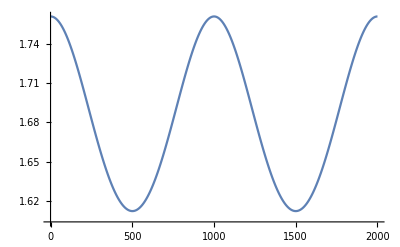

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.